## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="FBA1";
fitLabel=rxnName;
dataFileName =rxnName;
KeqEquilibrator=7.6×10^-4;

assumedUncertaintyFraction = 0.05;
removeInputFiles = True;
removeOutputFiles = True;
(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "fit";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data_model.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath, assumedUncertaintyFraction];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA1

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 8-10

Active sites:

Km Values:

Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
fdp | 0.00002 | 0.000019
0.000021 |  | M | 7.5 | 30 | trishcl | 0.05 | 
fdp | 0.00002 | 0.000018
0.000022 |  | M | 8 | 30 | trishcl | 0.05 | 
fdp | 0.00007 | 0.000058
0.000082 | cit | 0.011 | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
fdp | Null | 0.217 | 0.21
0.223 | 1/s | 8 | 30 | trishcl | 0.05 | 
fdp | Null
cit | 0.011 | 3.17 | 3.01
3.33 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

```mathematica
catalyticBranch={"E_FBA1[c] + fdp[c] <=> E_FBA1[c]&fdp",
				"E_FBA1[c]&fdp <=> E_FBA1[c]&dhap&g3p",
				"E_FBA1[c]&dhap&g3p <=> E_FBA1[c]&dhap + g3p[c]",
				"E_FBA1[c]&dhap <=> E_FBA1[c] + dhap[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["cit","c"]},ActivationSites->1,Inhibitors->{},InhibitionSites->0];
nActiveSites=8;
enzymeModel["Reactions"]
```

{((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA11,((FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c)^FBA12,((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA13,((FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c)^FBA14,((FBA1^c)_^(cit^c)+fdp^c⇌(FBA1^c&fdp^c)_^(cit^c))^FBA11$3,((FBA1^c&dhap^c)_^(cit^c)⇌(FBA1^c)_^(cit^c)+dhap^c)^FBA12$3,((FBA1^c&fdp^c)_^(cit^c)⇌(FBA1^c&dhap^c&g3p^c)_^(cit^c))^FBA13$3,((FBA1^c&dhap^c&g3p^c)_^(cit^c)⇌(FBA1^c&dhap^c)_^(cit^c)+g3p^c)^FBA14$3,((FBA1^c)_^+cit^c⇌(FBA1^c)_^(cit^c))^FBA1_Activation_cit$7}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBA1^c)_^+fdp^c⇌(FBA1^c&fdp^c)_^)^FBA11,Overscript[(FBA1^c&dhap^c)_^⇌(FBA1^c)_^+dhap^c, FBA12],((FBA1^c&fdp^c)_^⇌(FBA1^c&dhap^c&g3p^c)_^)^FBA13,Overscript[(FBA1^c&dhap^c&g3p^c)_^⇌(FBA1^c&dhap^c)_^+g3p^c, FBA14]};
catalyticReactionsSet2={Overscript[(FBA1^c)_^(cit^c)+fdp^c⇌(FBA1^c&fdp^c)_^(cit^c), FBA11$10],Overscript[(FBA1^c&dhap^c)_^(cit^c)⇌(FBA1^c)_^(cit^c)+dhap^c, FBA12$10],Overscript[(FBA1^c&fdp^c)_^(cit^c)⇌(FBA1^c&dhap^c&g3p^c)_^(cit^c), FBA13$10],Overscript[(FBA1^c&dhap^c&g3p^c)_^(cit^c)⇌(FBA1^c&dhap^c)_^(cit^c)+g3p^c, FBA14$10]};
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2};
```

### Setup King-Altmann Equations

#### Define some parameters

```mathematica
MWCFlag=False;
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};
```

```mathematica
{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,
		absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyMaxTime, nActiveSites];
```

kcat for

kcat rev

km for

km rev

## Semi-Automated Simulate Data

```mathematica
haldaneDataList=Table[
	{haldaneRatio, KeqEquilibrator,{0.9*KeqEquilibrator,1.1*KeqEquilibrator}},
{haldaneRatio, haldaneRatiosList}];

customRatiosDataList={};
```

### Simulate data

```mathematica
Export["FBA1SimulateDataArguments.mx",{enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["FBA1SimulateDataResults.mx",{allFittingData, dataPath, fileList, fileListSub},"MX"];
```

```mathematica
{allFittingData, dataPath, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0203403,0.0144975,0.0144975}

```mathematica
FilePrint@dataPath
```

dhap[c]	fdp[c]	g3p[c]	cit[c]	param_FBA1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.00076
0	2.0000000000000003e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.09090909090909091
0	3.1697863849222286e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.13680688860321005
0	5.023772863019165e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310186
0	7.96214341106994e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.2847472489508013
0	0.000012619146889603861	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.3868631798468569
0	0.00002	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.49999999999999994
0	0.00003169786384922229	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531432
0	0.00005023772863019165	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491988
0	0.00007962143411069939	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868981
0	0.0001261914688960386	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.86319311139679
0	0.00020000000000000004	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909092
0	2.0000000000000003e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.09090909090909091
0	3.1697863849222286e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.13680688860321005
0	5.023772863019165e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310186
0	7.96214341106994e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.2847472489508013
0	0.000012619146889603861	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.3868631798468569
0	0.00002	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.49999999999999994
0	0.00003169786384922229	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531432
0	0.00005023772863019165	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491988
0	0.00007962143411069939	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868981
0	0.0001261914688960386	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.86319311139679
0	0.00020000000000000004	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909092
0	7.000000000000002e-6	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.09090909090909094
0	0.000011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.13680688860321008
0	0.00001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310194
0	0.000027867501938744792	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.2847472489508013
0	0.000044167014113613516	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.3868631798468569
0	0.00007000000000000002	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.5000000000000001
0	0.00011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531432
0	0.0001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491989
0	0.0002786750193874482	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868984
0	0.0004416701411361352	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.86319311139679
0	0.0007000000000000001	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909092
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17

### Simulate data with uncertainty

```mathematica
Export["FBA1SimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, KeqName,allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["FBA1SimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
Get["MASSef`"];

nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, KeqName,allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0203403,0.0144975,0.0144975}

{0.0203403,0.0144975,0.0144975}

{0.0203403,0.0144975,0.0144975}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	fdp[c]	g3p[c]	cit[c]	param_FBA1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	0.0007213665017762222
0	1.8406103516902621e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.09090909090909088
0	2.9171708163673538e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.13680688860321003
0	4.62340416810685e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310186
0	7.327601792028872e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.2847472489508012
0	0.00001161346619725242	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.38686317984685675
0	0.000018406103516902623	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.5
0	0.000029171708163673538	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531431
0	0.0000462340416810685	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491987
0	0.00007327601792028871	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868981
0	0.0001161346619725242	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.8631931113967898
0	0.00018406103516902623	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909091
0	2.535603857550961e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.090909090909091
0	4.018661292610659e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.13680688860321016
0	6.369148925465615e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310203
0	0.000010094420773741472	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.28474724895080183
0	0.00001599857876614088	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.3868631798468571
0	0.00002535603857550961	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.5000000000000001
0	0.00004018661292610659	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531434
0	0.00006369148925465614	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491989
0	0.00010094420773741462	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868986
0	0.0001599857876614088	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.8631931113967901
0	0.0002535603857550961	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909093
0	5.686522076645088e-6	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.09090909090909097
0	9.012530128054638e-6	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.1368068886032101
0	0.00001428389764680449	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310197
0	0.000022638452142231762	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.28474724895080183
0	0.00003587952868807977	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.386863179846857
0	0.00005686522076645088	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.5000000000000001
0	0.00009012530128054638	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531433
0	0.00014283897646804488	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491988
0	0.0002263845214223174	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868985
0	0.00035879528688079773	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.8631931113967901
0	0.0005686522076645089	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909092
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217677076113374
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.1757202284997286

### Parameter scan

```mathematica
Export["FBA1ParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["FBA1ParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
Get["MASSef`"];
Get["MASSef`"];
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{10^-20,10^-18,10^-1}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneDataList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0203403,0.0144975,0.0144975}

{0.0203403,0.0144975,0.0144975}

{0.0203403,0.0144975,0.0144975}

«12 more identical outputs»

```mathematica
FilePrint@dataPathList[[14]]
```

dhap[c]	fdp[c]	g3p[c]	cit[c]	param_FBA1_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	0	0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_2.txt"	1.e-18
0	2.0000000000000003e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.09090909090909091
0	3.1697863849222286e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.13680688860321005
0	5.023772863019165e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310186
0	7.96214341106994e-6	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.2847472489508013
0	0.000012619146889603861	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.3868631798468569
0	0.00002	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.49999999999999994
0	0.00003169786384922229	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531432
0	0.00005023772863019165	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491988
0	0.00007962143411069939	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868981
0	0.0001261914688960386	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.86319311139679
0	0.00020000000000000004	0	0	1	7.5	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909092
0	2.0000000000000003e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.09090909090909091
0	3.1697863849222286e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.13680688860321005
0	5.023772863019165e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310186
0	7.96214341106994e-6	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.2847472489508013
0	0.000012619146889603861	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.3868631798468569
0	0.00002	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.49999999999999994
0	0.00003169786384922229	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531432
0	0.00005023772863019165	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491988
0	0.00007962143411069939	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868981
0	0.0001261914688960386	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.86319311139679
0	0.00020000000000000004	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909092
0	7.000000000000002e-6	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.09090909090909094
0	0.000011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.13680688860321008
0	0.00001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.20076000891310194
0	0.000027867501938744792	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.2847472489508013
0	0.000044167014113613516	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.3868631798468569
0	0.00007000000000000002	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.5000000000000001
0	0.00011094252347227801	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.6131368201531432
0	0.0001758320502056708	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7152527510491989
0	0.0002786750193874482	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.7992399910868984
0	0.0004416701411361352	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.86319311139679
0	0.0007000000000000001	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateFor_fdp.txt"	0.9090909090909092
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	0.217
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17
0	0.01	0	0.011	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateFor.txt"	3.17

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=1;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/haldaneRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme1/fit/input/haldaneRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"] //AbsoluteTiming
```

{53.9959,best_fit: 8.01348237122}

### Run Fitting on your Local System with uncertainty

```mathematica
Do[
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python",
						"\""<>runFitScriptPath <>"\"",
						 "\""<>psoParameterPath <>"\"",
						 "\""<>lmaParameterPath <>"\"", 
						"\""<> StringTake[psoTrialSummaryFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						"\""<> StringTake[psoResultsFileName, ;;-5] <>"_"<>ToString[datasetI] <>".txt\"",
						 "\""<>StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt\"", ToString @numTrials, 
						"\""<>dataPathList[[datasetI]] <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"] ,

{datasetI, 1, Length@dataPathList}];
```

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
lmaResultsFileNameOld=lmaResultsFileName;
lmaResultsFileName=StringTake[lmaResultsFileNameOld,;;-5]<>"_"<>ToString[1] <>".txt\""
```

```mathematica
splitChar = If[$OperatingSystem == "Windows", "\\", "/"];
resultsFileName = StringSplit[lmaResultsFileName, splitChar][[-1]];
fittingData = Import[dataPath];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw",resultsFileName}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_1 | 0.0000334241 | 1.11717×10^-9 | 0.00769648 | 0.00076 | 0.000760058
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
haldaneRatio_2 | 25.1327 | 631.655 | 100. | 0.00076 | 5.59841×10^-29
relRateFor_fdp | 0.0338777 | 0.0011477 | 7.50414 | 0.0909091 | 0.0840871
relRateFor_fdp | 0.0322292 | 0.00103872 | 7.15237 | 0.136807 | 0.127022
relRateFor_fdp | 0.0299217 | 0.000895307 | 6.65774 | 0.20076 | 0.187394
relRateFor_fdp | 0.0268726 | 0.000722136 | 6.00009 | 0.284747 | 0.267662
relRateFor_fdp | 0.0231363 | 0.000535287 | 5.18791 | 0.386863 | 0.366793
relRateFor_fdp | 0.0189588 | 0.000359437 | 4.27152 | 0.5 | 0.478642
relRateFor_fdp | 0.0147408 | 0.000217292 | 3.33724 | 0.613137 | 0.592675
relRateFor_fdp | 0.0108982 | 0.000118771 | 2.47818 | 0.715253 | 0.697528
relRateFor_fdp | 0.00771207 | 0.000059476 | 1.7601 | 0.79924 | 0.785173
relRateFor_fdp | 0.00527018 | 0.0000277748 | 1.20617 | 0.863193 | 0.852782
relRateFor_fdp | 0.00350919 | 0.0000123144 | 0.804765 | 0.909091 | 0.901775
relRateFor_fdp | 0.0338777 | 0.0011477 | 7.50414 | 0.0909091 | 0.0840871
relRateFor_fdp | 0.0322292 | 0.00103872 | 7.15237 | 0.136807 | 0.127022
relRateFor_fdp | 0.0299217 | 0.000895307 | 6.65774 | 0.20076 | 0.187394
relRateFor_fdp | 0.0268726 | 0.000722136 | 6.00009 | 0.284747 | 0.267662
relRateFor_fdp | 0.0231363 | 0.000535287 | 5.18791 | 0.386863 | 0.366793
relRateFor_fdp | 0.0189588 | 0.000359437 | 4.27152 | 0.5 | 0.478642
relRateFor_fdp | 0.0147408 | 0.000217292 | 3.33724 | 0.613137 | 0.592675
relRateFor_fdp | 0.0108982 | 0.000118771 | 2.47818 | 0.715253 | 0.697528
relRateFor_fdp | 0.00771207 | 0.000059476 | 1.7601 | 0.79924 | 0.785173
relRateFor_fdp | 0.00527018 | 0.0000277748 | 1.20617 | 0.863193 | 0.852782
relRateFor_fdp | 0.00350919 | 0.0000123144 | 0.804765 | 0.909091 | 0.901775
relRateFor_fdp | 0.146487 | 0.0214584 | 40.1157 | 0.0909091 | 0.127378
relRateFor_fdp | 0.137779 | 0.018983 | 37.3342 | 0.136807 | 0.187883
relRateFor_fdp | 0.125929 | 0.0158581 | 33.6377 | 0.20076 | 0.268291
relRateFor_fdp | 0.110843 | 0.0122861 | 29.0752 | 0.284747 | 0.367538
relRateFor_fdp | 0.0931792 | 0.00868236 | 23.9308 | 0.386863 | 0.479443
relRateFor_fdp | 0.0744132 | 0.00553733 | 18.6898 | 0.5 | 0.593449
relRateFor_fdp | 0.0564247 | 0.00318374 | 13.874 | 0.613137 | 0.698204
relRateFor_fdp | 0.0408044 | 0.001665 | 9.85109 | 0.715253 | 0.785713
relRateFor_fdp | 0.0283653 | 0.00080459 | 6.74936 | 0.79924 | 0.853184
relRateFor_fdp | 0.0191267 | 0.000365832 | 4.50251 | 0.863193 | 0.902058
relRateFor_fdp | 0.0126155 | 0.000159151 | 2.94743 | 0.909091 | 0.935886
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.892395 | 0.796369 | 680.54 | 0.217 | 1.69377
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936
absRateFor | 0.273337 | 0.0747132 | 46.7079 | 3.17 | 1.68936

### Simulated Data and Best Fit Data Plot

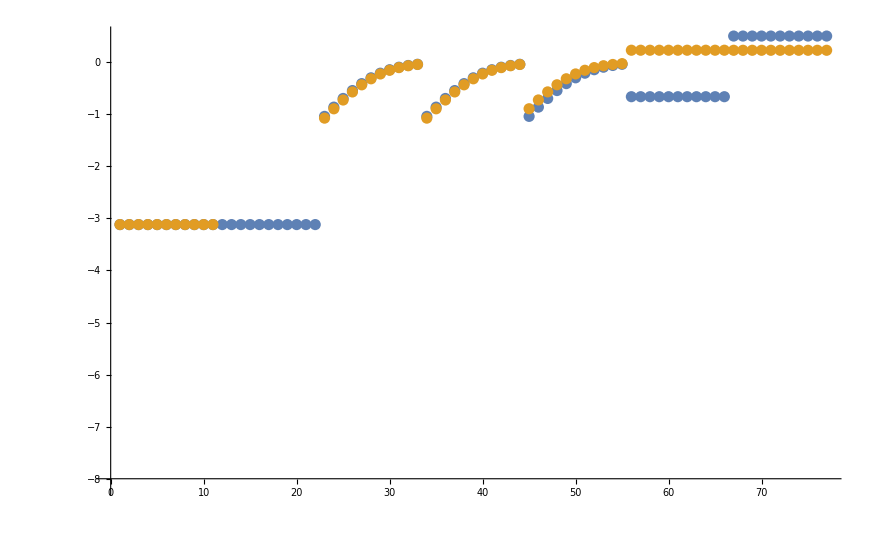

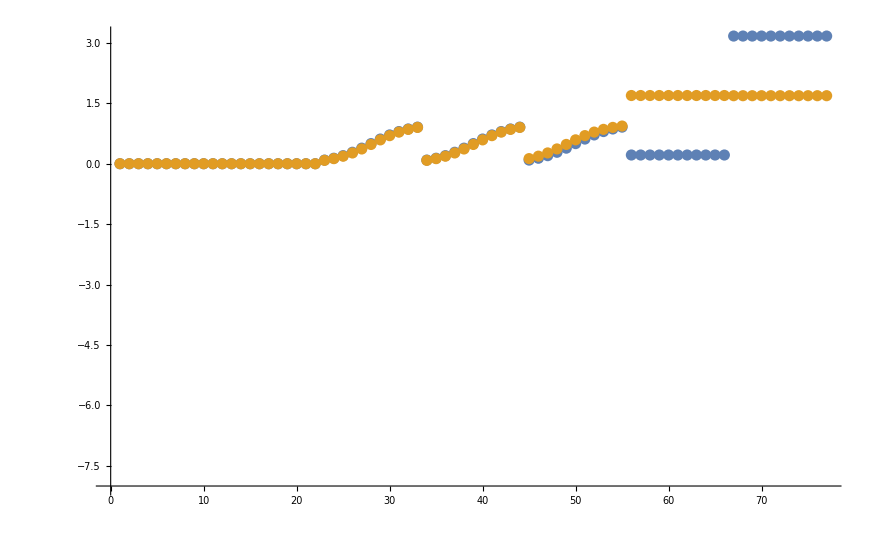

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

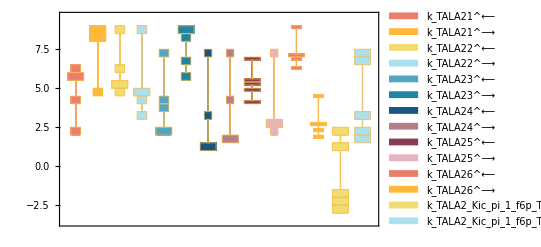

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

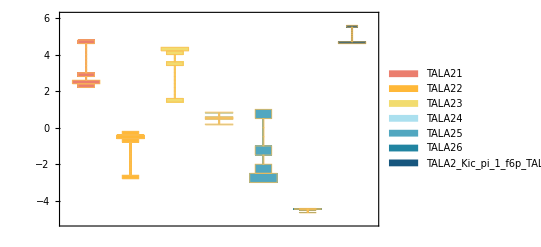

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

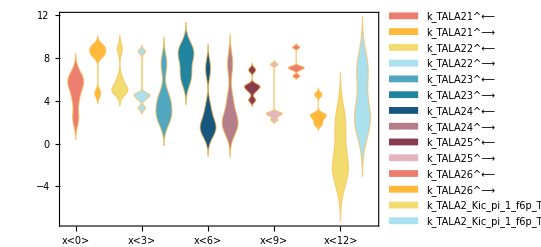

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

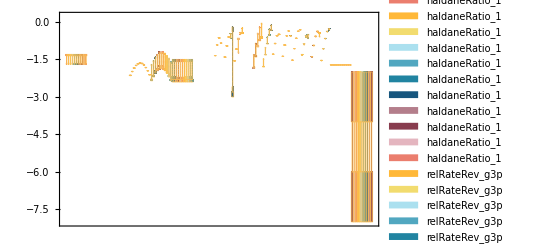

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList[[{1,2,4,5}]], absoluteRateForward/.m["pi","c"]-> 0, absoluteRateReverse/.m["pi","c"]-> 0, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000038 | 0.000035798 | 5.79467
0.00009 | 0.0000219601 | 75.5999
0.0012 | 0.00131506 | 9.58806
0.000285 | 0.000301835 | 5.90696

```mathematica
backCalculateRatios[haldaneRatiosList[[1]][[1]], haldaneRatiosList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.840336 | 0.791753 | 5.78138

```mathematica
backCalculateRatios[haldaneRatiosList[[2]][[1]], haldaneRatiosList[[2]][[2]], paramFitSub]//TableForm
```